```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[(a/y[t])Sqrt[1-y'[t]^2]- q y[t],y[t],t]
```

-(a+q y[t]^2 √(1-y'[t]^2)-y'[t]^2 (a+q y[t]^2 √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0

1.

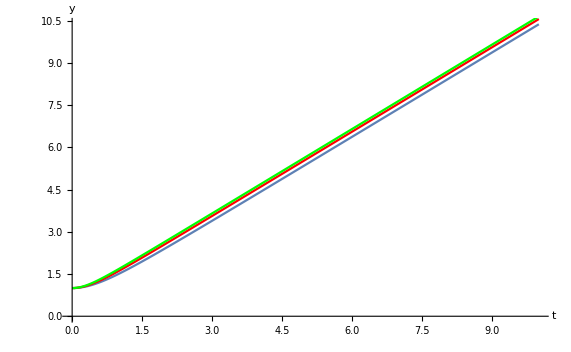

```mathematica
Block[
{y1,y2,dy,py,qcrit},
y1[a1_,ys_,q1_]:=NDSolveValue[{-(a+q y[t]^2 √(1-y'[t]^2)-y'[t]^2 (a+q y[t]^2 √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0/.{a->a1,q->q1},y[0]==ys,y'[0]==0},y[t],{t,0,10}];
y2[t1_,a_,ys_,q_]:=y1[a,ys,q]/.{t->t1};
qcrit[a_,ys_]:=a/ys^2;
dy[t1_,a_,ys_,q_]:=D[y1[a,ys,q],t]/.{t->t1};
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[qcrit[1,1]//N];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,1,0.32qcrit[1,1]]},{i,0,10,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,1,0.82qcrit[1,1]]},{i,0,10,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,1,1.32qcrit[1,1]]},{i,0,10,0.05}],AxesLabel->{t,y},PlotStyle->Green]
]
];
]
```

0.01

0.00694444

0.00510204

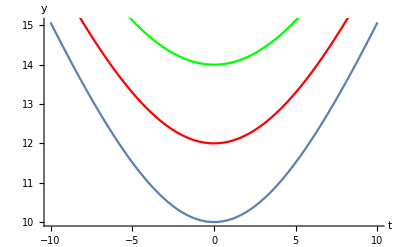

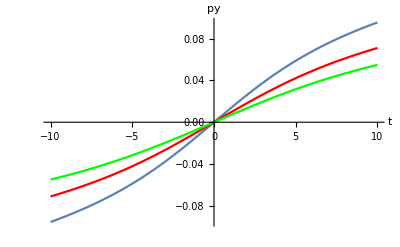

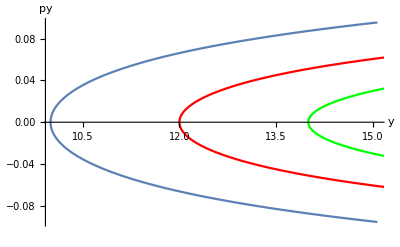

```mathematica
Block[
{y1,y2,dy,py,qcrit},
y1[a1_,ys_,q1_]:=NDSolveValue[{-(a+q y[t]^2 √(1-y'[t]^2)-y'[t]^2 (a+q y[t]^2 √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0/.{a->a1,q->q1},y[0]==ys,y'[0]==0},y[t],{t,-10,10}];
y2[t1_,a_,ys_,q_]:=y1[a,ys,q]/.{t->t1};
qcrit[a_,ys_]:=a/ys^2;
dy[t1_,a_,ys_,q_]:=D[y1[a,ys,q],t]/.{t->t1};
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[qcrit[1,10]//N];
Print[qcrit[1,12]//N];
Print[qcrit[1,14]//N];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,10,0.32qcrit[1,10]]},{i,-10,10,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,12,0.32qcrit[1,12]]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,14,0.32qcrit[1,14]]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Green]
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,10,0.32qcrit[1,10]]},{i,-10,10,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,12,0.32qcrit[1,12]]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,14,0.32qcrit[1,14]]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Green]
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,10,0.32qcrit[1,10]],py[i,1,10,0.32qcrit[1,10]]},{i,-10,10,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,12,0.32qcrit[1,12]],py[i,1,12,0.32qcrit[1,12]]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,14,0.32qcrit[1,14]],py[i,1,14,0.32qcrit[1,14]]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Green]
]
];
]
```

0.01

0.00694444

0.00510204

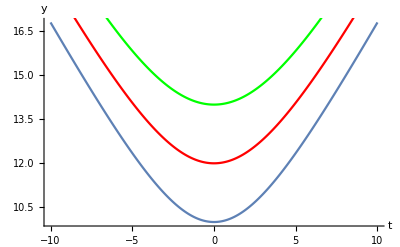

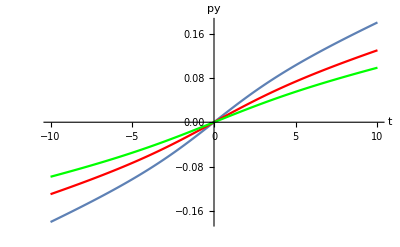

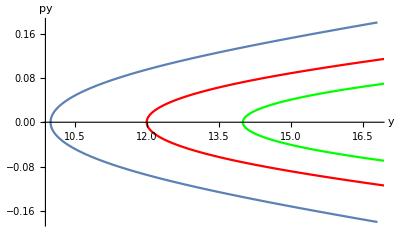

```mathematica
Block[
{y1,y2,dy,py,qcrit},
y1[a1_,ys_,q1_]:=NDSolveValue[{-(a+q y[t]^2 √(1-y'[t]^2)-y'[t]^2 (a+q y[t]^2 √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0/.{a->a1,q->q1},y[0]==ys,y'[0]==0},y[t],{t,-10,10}];
y2[t1_,a_,ys_,q_]:=y1[a,ys,q]/.{t->t1};
qcrit[a_,ys_]:=a/ys^2;
dy[t1_,a_,ys_,q_]:=D[y1[a,ys,q],t]/.{t->t1};
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[qcrit[1,10]//N];
Print[qcrit[1,12]//N];
Print[qcrit[1,14]//N];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,10,1.32qcrit[1,10]]},{i,-10,10,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,12,1.32qcrit[1,12]]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,14,1.32qcrit[1,14]]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Green]
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,10,1.32qcrit[1,10]]},{i,-10,10,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,12,1.32qcrit[1,12]]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,14,1.32qcrit[1,14]]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Green]
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,10,1.32qcrit[1,10]],py[i,1,10,1.32qcrit[1,10]]},{i,-10,10,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,12,1.32qcrit[1,12]],py[i,1,12,1.32qcrit[1,12]]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,14,1.32qcrit[1,14]],py[i,1,14,1.32qcrit[1,14]]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Green]
]
];
]
```